```mathematica
ClearAll["Global`*"]
z1=1+I Sqrt[3];
{Re[z1],Im[z1],Abs[z1],Arg[z1]}
Assuming[0≤α<2 Pi,z2=1-Cos[α]+I Sin[α];
{ComplexExpand[Re[z2]],ComplexExpand[Im[z2]],FullSimplify[Abs[z2]],FullSimplify[Arg[z2]]}]
Assuming[Element[x,Reals],z3=Exp[I Sin[x]];
{ComplexExpand[Re[z3]],ComplexExpand[Im[z3]],FullSimplify[Abs[z3]],FullSimplify[Arg[z3]]}]
```

{1,√3,2,π/3}

{1-Cos[α],Sin[α],Abs[1-Cos[α]+ⅈ Sin[α]],Arg[1-Cos[α]+ⅈ Sin[α]]}

{Cos[Sin[x]],Sin[Sin[x]],1,Sin[x]}

{-ⅈ,ⅈ}

{{0,-1},{0,1}}

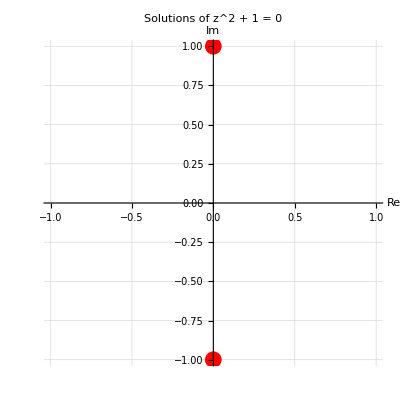

```mathematica
ClearAll["Global`*"]

sol1=z/.Solve[z^2+1==0,z]
pts1=({Re[#],Im[#]}&)/@sol1

ListPlot[pts1,AxesLabel->{"Re","Im"},PlotStyle->{Red,PointSize[0.03]},GridLines->Automatic,PlotRange->All,AspectRatio->1,PlotLabel->"Solutions of z^2 + 1 = 0"]
```

{-2,2 (-1)^(1/3),-2 (-1)^(2/3)}

{{-2,0},{1,√3},{1,-√3}}

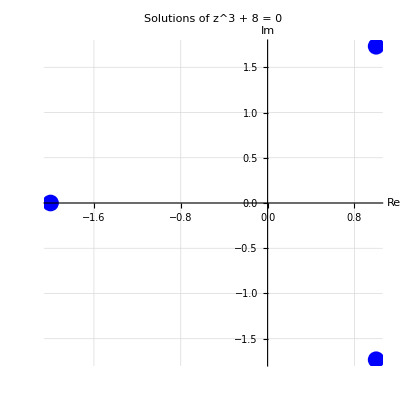

```mathematica
sol2=z/.Solve[z^3+8==0,z]
pts2=({Re[#],Im[#]}&)/@sol2

ListPlot[pts2,AxesLabel->{"Re","Im"},PlotStyle->{Blue,PointSize[0.03]},GridLines->Automatic,PlotRange->All,AspectRatio->1,PlotLabel->"Solutions of z^3 + 8 = 0"]
```

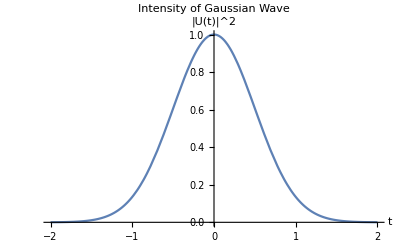

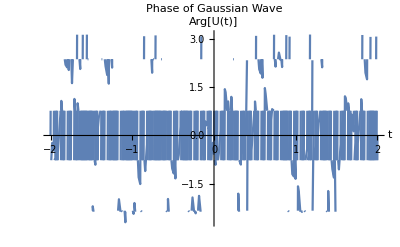

```mathematica
ClearAll["Global`*"]

T0=1;
ω0=200 Pi;

U[t_]:=Exp[-t^2/T0^2+I ω0 t];

(*强度*)
Plot[Abs[U[t]]^2,{t,-2,2},AxesLabel->{"t","|U(t)|^2"},PlotLabel->"Intensity of Gaussian Wave",PlotRange->All]

(*相位*)
Plot[Arg[U[t]],{t,-2,2},AxesLabel->{"t","Arg[U(t)]"},PlotLabel->"Phase of Gaussian Wave",PlotRange->All]
```

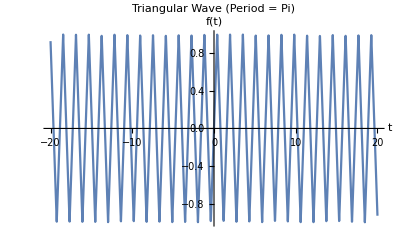

```mathematica
ClearAll["Global`*"]

tri[t_]:=TriangleWave[2 t/Pi]

Plot[tri[t],{t,-20,20},AxesLabel->{"t","f(t)"},PlotLabel->"Triangular Wave (Period = Pi)",PlotRange->All]
```

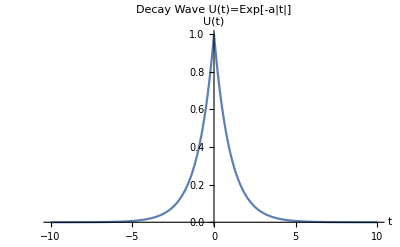

```mathematica
ClearAll["Global`*"]

a=1;
U[t_]:=Exp[-a Abs[t]];

Plot[U[t],{t,-10,10},AxesLabel->{"t","U(t)"},PlotLabel->"Decay Wave U(t)=Exp[-a|t|]",PlotRange->All]
```

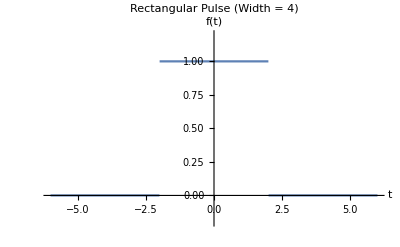

```mathematica
ClearAll["Global`*"]

rect[t_]:=Piecewise[{{1,Abs[t]≤2}},0]

Plot[rect[t],{t,-6,6},AxesLabel->{"t","f(t)"},PlotLabel->"Rectangular Pulse (Width = 4)",PlotRange->{-0.2,1.2}]
```

```mathematica
ClearAll["Global`*"]

Integrate[Exp[I t]/Exp[I t]*I Exp[I t],{t,0,2 Pi}]
```

0

```mathematica
ClearAll["Global`*"]

z[t_]:=Exp[I t];
Integrate[(1/Abs[z[t]]) z'[t],{t,0,2 Pi}]
```

0

```mathematica
ClearAll["Global`*"]

f[z_]:=z Abs[z]^2

(*写成 x,y 形式*)
u[x_,y_]=ComplexExpand[Re[f[x+I y]]]
v[x_,y_]=ComplexExpand[Im[f[x+I y]]]

(*Cauchy-Riemann 条件*)
cr1=FullSimplify[D[u[x,y],x]==D[v[x,y],y]]
cr2=FullSimplify[D[u[x,y],y]==-D[v[x,y],x]]

(*联立求解*)
Solve[{D[u[x,y],x]==D[v[x,y],y],D[u[x,y],y]==-D[v[x,y],x]},{x,y},Reals]
```

x^3+x y^2

x^2 y+y^3

x^2==y^2

x y==0

{{x→0,y→0}}

```mathematica
Print["f(z)=z|z|^2 仅在 z=0 处满足 C-R 条件，因此仅在 z=0 处可导；在任何开区域内都不解析。"]
```

f(z)=z|z|^2 仅在 z=0 处满足 C-R 条件，因此仅在 z=0 处可导；在任何开区域内都不解析。

```mathematica
ClearAll["Global`*"]

expr=((Conjugate[z] z+2 z-Conjugate[z]-2)/(z^2-1));

exprXY=ComplexExpand[expr/.z->x+I y];

Limit[exprXY,{x,y}->{1,0}]
```

3/2

```mathematica
ClearAll["Global`*"]

an[n_]:=1/n^3;
R1=1/Limit[Abs[an[n]]^(1/n),n->Infinity]
```

1

```mathematica
ClearAll["Global`*"]

bn[n_]:=1/n!;
R2=Infinity
```

∞

```mathematica
ClearAll["Global`*"]

Series[Exp[z] Sin[z],{z,0,10}]
Normal[%]
```

z+z^2+z^3/3-z^5/30-z^6/90-z^7/630+z^9/22680+z^10/113400+O[z]^11

z+z^2+z^3/3-z^5/30-z^6/90-z^7/630+z^9/22680+z^10/113400

```mathematica
Series[Log[z+2],{z,0,10}]
Normal[%]
```

Log[2]+z/2-z^2/8+z^3/24-z^4/64+z^5/160-z^6/384+z^7/896-z^8/2048+z^9/4608-z^10/10240+O[z]^11

z/2-z^2/8+z^3/24-z^4/64+z^5/160-z^6/384+z^7/896-z^8/2048+z^9/4608-z^10/10240+Log[2]

```mathematica
Series[1/(1+z^2)^2,{z,0,10}]
Normal[%]
```

1-2 z^2+3 z^4-4 z^6+5 z^8-6 z^10+O[z]^11

1-2 z^2+3 z^4-4 z^6+5 z^8-6 z^10

```mathematica
SetOptions[FourierTransform,FourierParameters->{0,1}];
SetOptions[InverseFourierTransform,FourierParameters->{0,1}];
```

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

FourierTransform[Sin[t]^2,t,ω]
```

-1/2 √(π/2) DiracDelta[-2+ω]+√(π/2) DiracDelta[ω]-1/2 √(π/2) DiracDelta[2+ω]

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

f[t_]:=1/2 (DiracDelta[t+a]+DiracDelta[t-a]+DiracDelta[t+a/2]+DiracDelta[t-a/2]);

FourierTransform[f[t],t,ω]
```

(ⅇ^(-ⅈ a ω) (1+ⅇ^((ⅈ a ω)/2)+ⅇ^((3 ⅈ a ω)/2)+ⅇ^(2 ⅈ a ω)))/(2 √(2 π))

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

f[t_]:=DiracDelta[t-1] (t-2)^2 Cos[t];

FourierTransform[f[t],t,ω]
```

(ⅇ^(ⅈ ω) Cos[1])/(√(2 π))

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

FourierTransform[Sign[t],t,ω]
```

(ⅈ √(2/π))/ω

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

Assuming[β>0,FourierTransform[Exp[-β Abs[t]],t,ω]]
```

(√(2/π) β)/(β^2+ω^2)

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

FourierTransform[UnitStep[t] Cos[3 t],t,ω]
```

ⅈ/(2 √(2 π) (-3+ω))+ⅈ/(2 √(2 π) (3+ω))+1/2 √(π/2) DiracDelta[-3+ω]+1/2 √(π/2) DiracDelta[3+ω]

```mathematica
ClearAll["Global`*"]
SetOptions[InverseFourierTransform,FourierParameters->{0,1}];

InverseFourierTransform[1/(2+I ω),ω,t]
```

ⅇ^(2 t) √(2 π) HeavisideTheta[-t]

```mathematica
ClearAll["Global`*"]
SetOptions[InverseFourierTransform,FourierParameters->{0,1}];

InverseFourierTransform[(2 Sin[3 (ω-2 Pi)])/(ω-2 Pi),ω,t]
```

√(π/2) (Sign[3-t]+Sign[3+t]) (Cos[2 π t]-ⅈ Sin[2 π t])

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

f[t_,b_]:=Piecewise[{{2,Abs[t]≤b}},0]

F[ω_,b_]=FullSimplify[FourierTransform[f[t,b],t,ω]]
```

Piecewise[{{(2 √(2/π) Sin[b ω])/ω, b>0}, {0, True}}]

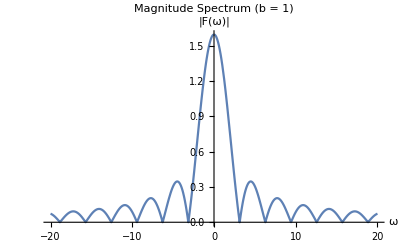

```mathematica
Plot[Evaluate[Abs[F[ω,1]]],{ω,-20,20},AxesLabel->{"ω","|F(ω)|"},PlotLabel->"Magnitude Spectrum (b = 1)",PlotRange->All]
```

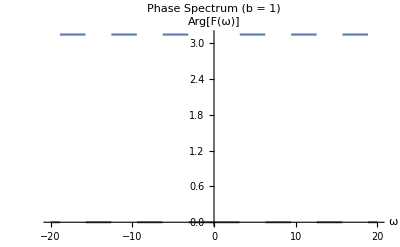

```mathematica
Plot[Evaluate[Arg[F[ω,1]]],{ω,-20,20},AxesLabel->{"ω","Arg[F(ω)]"},PlotLabel->"Phase Spectrum (b = 1)",PlotRange->All]
```

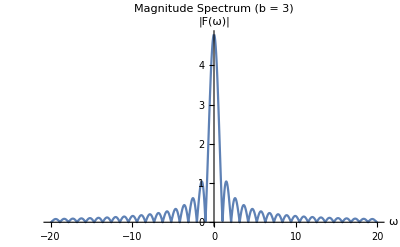

```mathematica
Plot[Evaluate[Abs[F[ω,3]]],{ω,-20,20},AxesLabel->{"ω","|F(ω)|"},PlotLabel->"Magnitude Spectrum (b = 3)",PlotRange->All]
```

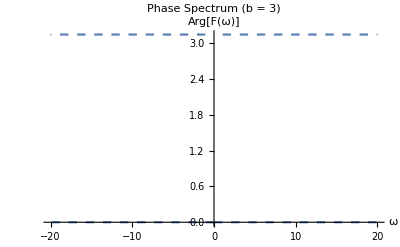

```mathematica
Plot[Evaluate[Arg[F[ω,3]]],{ω,-20,20},AxesLabel->{"ω","Arg[F(ω)]"},PlotLabel->"Phase Spectrum (b = 3)",PlotRange->All]
```

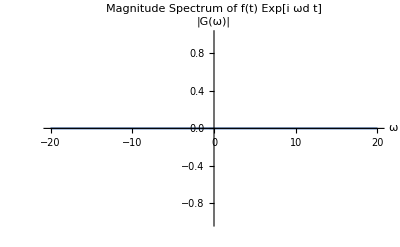

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

b=1;
ωd=4;

g[t_]:=f[t,b] Exp[I ωd t];
G[ω_]=FullSimplify[FourierTransform[g[t],t,ω]]

Plot[Evaluate[Abs[G[ω]]],{ω,-20,20},AxesLabel->{"ω","|G(ω)|"},PlotLabel->"Magnitude Spectrum of f(t) Exp[i ωd t]",PlotRange->All]
```

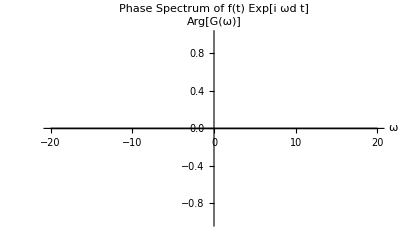

```mathematica
Plot[Evaluate[Arg[G[ω]]],{ω,-20,20},AxesLabel->{"ω","Arg[G(ω)]"},PlotLabel->"Phase Spectrum of f(t) Exp[i ωd t]",PlotRange->All]
```

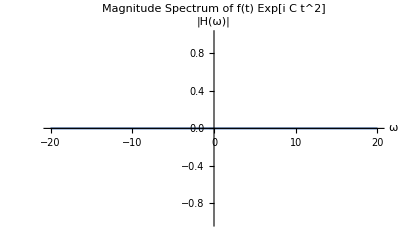

```mathematica
ClearAll["Global`*"]
SetOptions[FourierTransform,FourierParameters->{0,1}];

b=1;
C=1;

h[t_]:=f[t,b] Exp[I C t^2];

H[ω_]=FourierTransform[h[t],t,ω];

Plot[Evaluate[Abs[H[ω]]],{ω,-20,20},AxesLabel->{"ω","|H(ω)|"},PlotLabel->"Magnitude Spectrum of f(t) Exp[i C t^2]",PlotRange->All]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at t = ∞.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{-∞,∞}}. NIntegrate obtained 0.+0. ⅈ and 0. for the integral and error estimates.

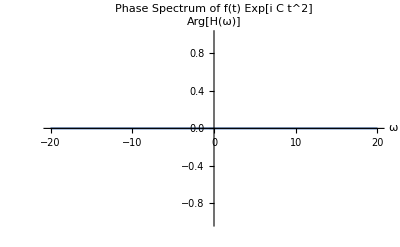

```mathematica
Plot[Evaluate[Arg[H[ω]]],{ω,-20,20},AxesLabel->{"ω","Arg[H(ω)]"},PlotLabel->"Phase Spectrum of f(t) Exp[i C t^2]",PlotRange->All]
```